```mathematica
ClearAll
```

ClearAll

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma[a_]=gamma0+gammap0(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma[a];
```

```mathematica
om=0.3;
gamma0=0.55;
gammap0=-0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

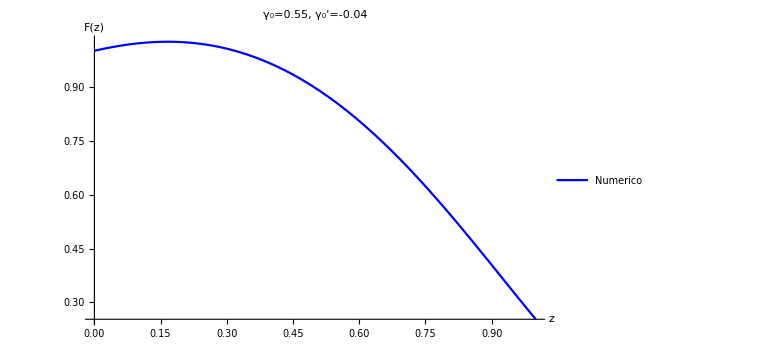

```mathematica
p1=Plot[Fz[z],{z,0,1}, PlotLegends->{"Numerico"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["F(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Blue}, ImageSize->Large, PlotLabel->Style["γ_0=0.55, γ_0'=-0.04", Black, FontSize->20]]
```

```mathematica
points=Table[{z,Fz[z]},{z,0,1,0.01}];
```

```mathematica
fit1=Fit[points, {1,z,z^2},z];
res1=Fit[points, {1,z,z^2},z,"FitResiduals"];
pointsfit=Table[{z,fit1},{z,0,1,0.01}];
```

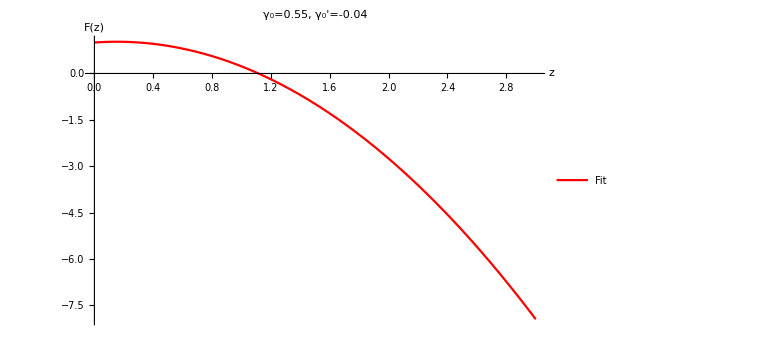

```mathematica
fit=Plot[fit1,{z,0,3}, PlotLegends->{"Fit"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["F(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Red}, ImageSize->Large, PlotLabel->Style["γ_0=0.55, γ_0'=-0.04", Black, FontSize->20]]
```

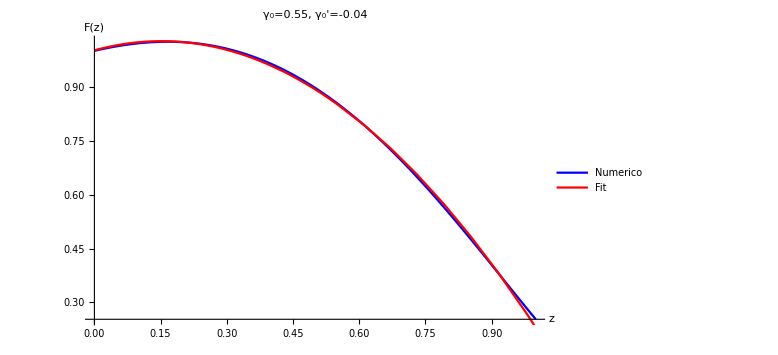

```mathematica
Show[p1,fit]
```

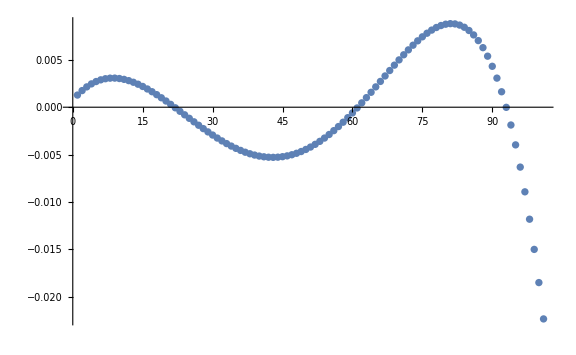

```mathematica
plotres1=ListPlot[res1, ImageSize->Large]
```

```mathematica
dif[z_]=1-fit1/Fz[z]
```

1-(1.00128+0.336927 z-1.10728 z^2)/(InterpolatingFunction[…][1/(1+z)])

```mathematica
Res6=Table[{z,dif[z]},{z,0,1,0.01}];
```

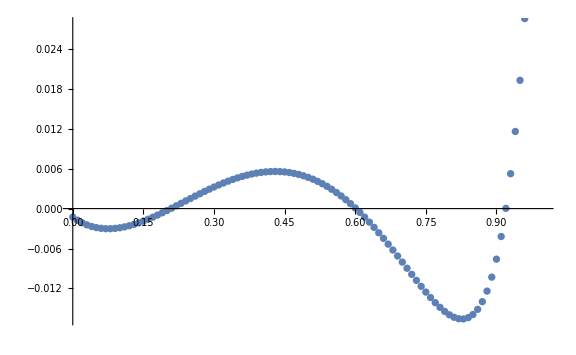

```mathematica
ListPlot[Res6, ImageSize->Large]
```

```mathematica
PearsonChiSquareTest[pointsfit,points]
```

0.999988

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
Fpoly[z_]:=1.001283893224917+0.3369271691259142 z-1.1072791685116707 z^2
```

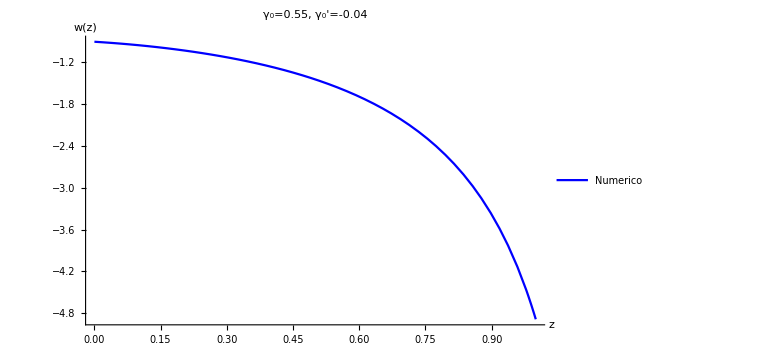

```mathematica
wnum=Plot[w[z],{z,0,1},PlotLegends->{"Numerico"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Blue}, ImageSize->Large, PlotLabel->Style["γ_0=0.55, γ_0'=-0.04", Black, FontSize->20]]
```

```mathematica
wpoly[z_]:=Fpoly'[z]/Fpoly[z] 1/3(1+z)-1;
```

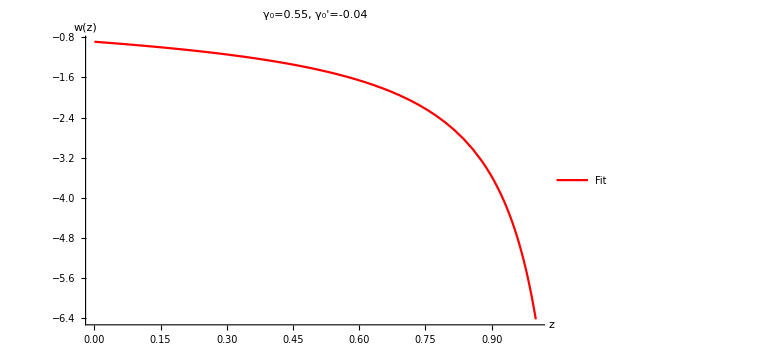

```mathematica
wpol=Plot[wpoly[z],{z,0,1},PlotLegends->{"Fit"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Red}, ImageSize->Large, PlotLabel->Style["γ_0=0.55, γ_0'=-0.04", Black, FontSize->20]]
```

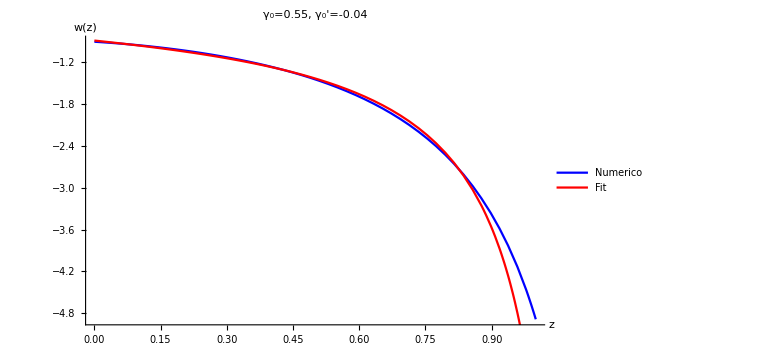

```mathematica
plot1=Show[wnum,wpol]
```

```mathematica
wnumtable=Table[{z,w[z]},{z,0,1,0.01}];
wpoltable=Table[{z,wpoly[z]},{z,0,1,0.01}];
```

```mathematica
dif1[z_]=1-wpoly[z]/w[z];
Res7=Table[{z,dif1[z]},{z,0,1,0.01}];
```

```mathematica
errorplot1=Plot[0.05,{z,0,1}, PlotStyle->{Thick, Dashed, Black}];
errorplot2=Plot[-0.05,{z,0,1}, PlotStyle->{Thick, Dashed, Black}];
```

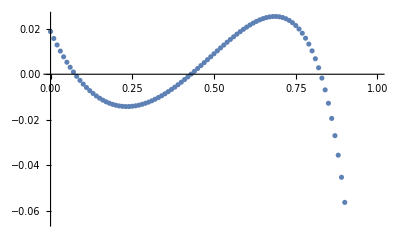

```mathematica
plotres=ListPlot[Res7]
```

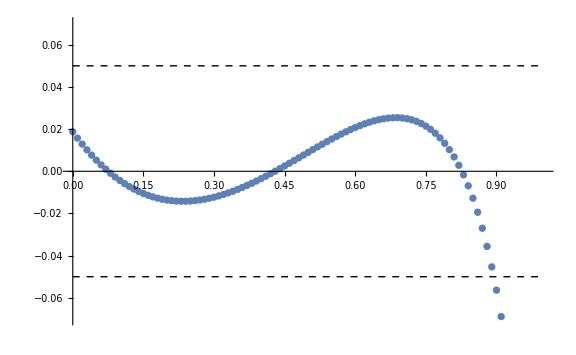

```mathematica
plot2=Show[plotres,errorplot1,errorplot2, PlotRange->{-0.07,0.07}, ImageSize->Large]
```

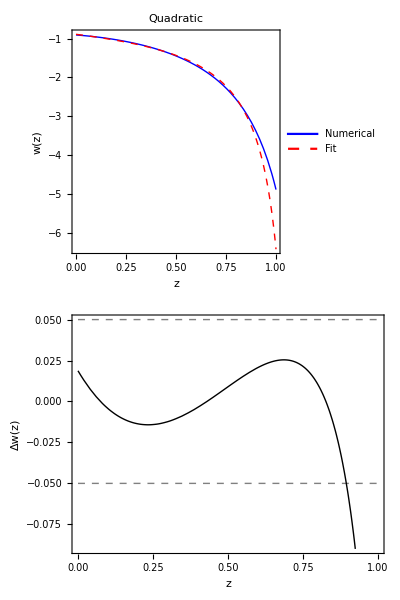

```mathematica
col1=Column[{Plot[{w[z],wpoly[z]},{z,0,1},ImagePadding->{{100,4},{1,1}} ,PlotStyle->{{Thick,Blue},{Thick,Dashed,Red}}, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["w(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"Numerical", "Fit"},LegendFunction->"Frame", Background->White],{Left,Bottom}], PlotLabel->Style["Quadratic", Black, FontSize->20]],Plot[{0.05,-0.05, dif1[z]},{z,0,1},ImagePadding->{{100,4},{70,0}},PlotStyle->{{Thick,Dashed,Gray},{Thick,Dashed,Gray}, {Thick, Black}}, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["Δw(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, AspectRatio->1/4, PlotRange->{0.09,-0.09}]}, Spacings->0]
```

```mathematica
Clear
ClearAll
ClearAttributes
ClearCookies
```

Clear

ClearAll

ClearAttributes

ClearCookies

```mathematica
fit2=Fit[points, {1,z,z^2,z^3},z]
```

0.990883+0.464927 z-1.42888 z^2+0.214398 z^3

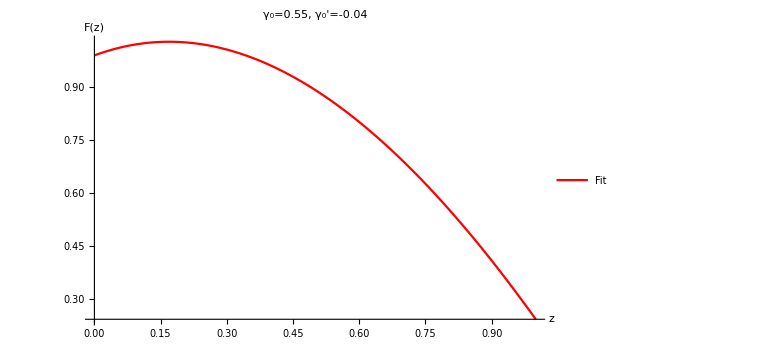

```mathematica
fit=Plot[fit2,{z,0,1}, PlotLegends->{"Fit"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["F(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Red}, ImageSize->Large, PlotLabel->Style["γ_0=0.55, γ_0'=-0.04", Black, FontSize->20]]
```

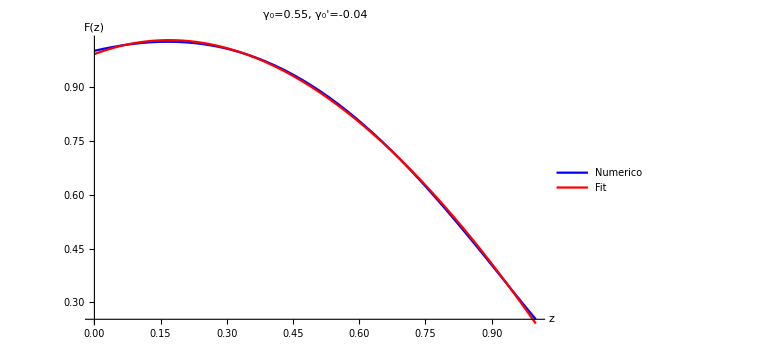

```mathematica
Show[p1,fit]
```

```mathematica
pointsfit2=Table[{z,fit2},{z,0,1,0.01}];
PearsonChiSquareTest[pointsfit2,points]
```

0.999848

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
Fpoly[z_]:=0.9908834540260197+0.46492696732270133 z-1.4288759279086425 z^2+0.21439783959798006 z^3
```

```mathematica
wnum=Plot[w[z],{z,0,1},PlotLegends->{"Numerico"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Blue}, ImageSize->Large, PlotLabel->Style["γ_0=0.55, γ_0'=-0.04", Black, FontSize->20]]
```

-Graphics-

```mathematica
wpoly[z_]:=Fpoly'[z]/Fpoly[z] 1/3(1+z)-1;
```

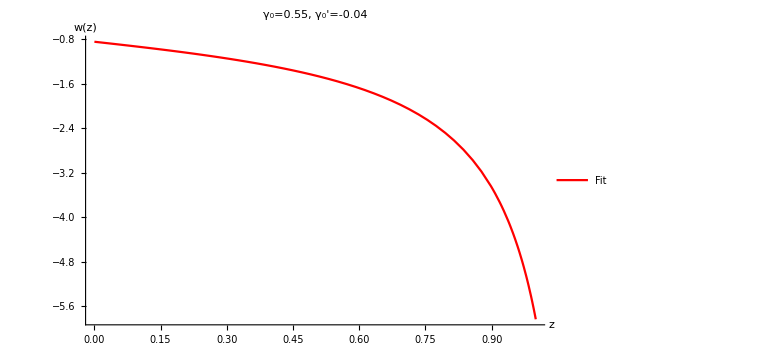

```mathematica
wpol=Plot[wpoly[z],{z,0,1},PlotLegends->{"Fit"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Red}, ImageSize->Large, PlotLabel->Style["γ_0=0.55, γ_0'=-0.04", Black, FontSize->20]]
```

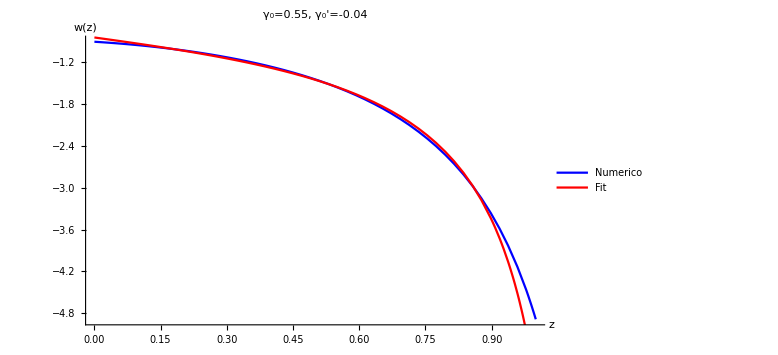

```mathematica
Show[wnum,wpol]
```

```mathematica
wnumtable=Table[{z,w[z]},{z,0,1,0.01}];
wpoltable=Table[{z,wpoly[z]},{z,0,1,0.01}];
dif1[z_]=1-wpoly[z]/w[z];
Res7=Table[{z,dif1[z]},{z,0,1,0.01}];
plotres=ListPlot[Res7];
errorplot1=Plot[0.05,{z,0,1}, PlotStyle->{Thick, Dashed, Black}];
errorplot2=Plot[-0.05,{z,0,1}, PlotStyle->{Thick, Dashed, Black}];
```

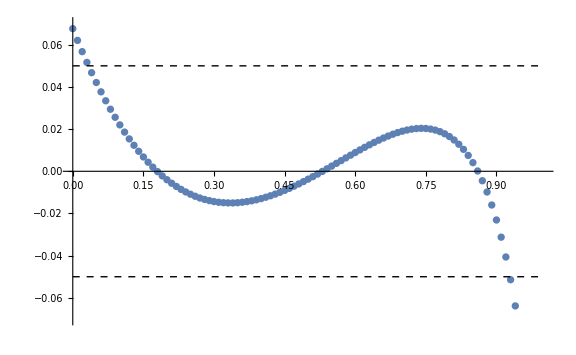

```mathematica
Show[plotres,errorplot1,errorplot2, PlotRange->{-0.07,0.07}, ImageSize->Large]
```

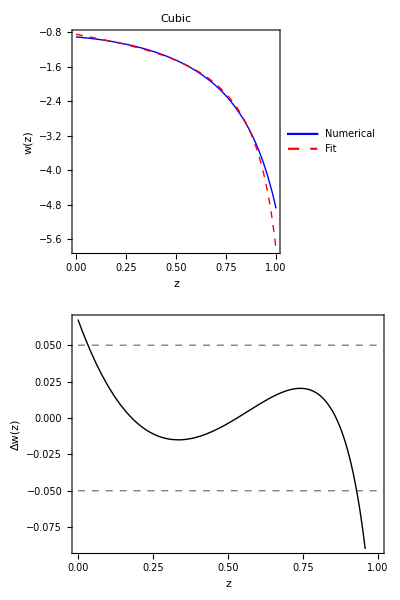

```mathematica
col2=Column[{Plot[{w[z],wpoly[z]},{z,0,1},ImagePadding->{{100,4},{1,1}} ,PlotStyle->{{Thick,Blue},{Thick,Dashed,Red}}, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["w(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"Numerical", "Fit"},LegendFunction->"Frame", Background->White],{Left,Bottom}], PlotLabel->Style["Cubic", Black, FontSize->20]],Plot[{0.05,-0.05, dif1[z]},{z,0,1},ImagePadding->{{100,4},{70,0}},PlotStyle->{{Thick,Dashed,Gray},{Thick,Dashed,Gray}, {Thick, Black}}, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["Δw(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, AspectRatio->1/4, PlotRange->{0.09,-0.09}]}, Spacings->0]
```

```mathematica
Clear
ClearAll
ClearAttributes
ClearCookies
```

Clear

ClearAll

ClearAttributes

ClearCookies

```mathematica
fit3=Fit[points, {1,z,z^2,z^3,z^4},z]
```

1.00122+0.248463 z-0.443444 z^2-1.32354 z^3+0.768967 z^4

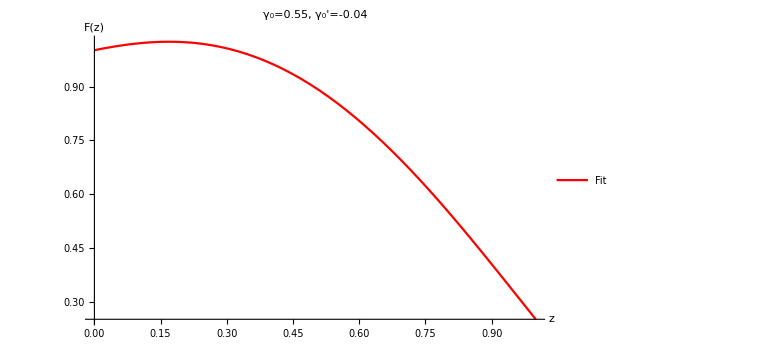

```mathematica
fit=Plot[fit3,{z,0,1}, PlotLegends->{"Fit"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["F(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Red}, ImageSize->Large, PlotLabel->Style["γ_0=0.55, γ_0'=-0.04", Black, FontSize->20]]
```

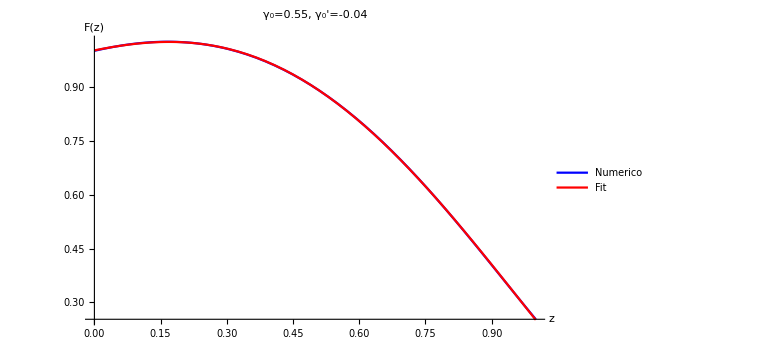

```mathematica
Show[p1,fit]
```

```mathematica
pointsfit3=Table[{z,fit3},{z,0,1,0.01}];
PearsonChiSquareTest[pointsfit3,points]
```

1.

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
Fpoly[z_]:=1.0012216043534157+0.24846266917464244 z-0.44344431839980764 z^2-1.3235367831235743 z^3+0.7689673113607776 z^4
```

```mathematica
wnum=Plot[w[z],{z,0,1},PlotLegends->{"Numerico"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Blue}, ImageSize->Large, PlotLabel->Style["γ_0=0.55, γ_0'=-0.04", Black, FontSize->20]]
```

-Graphics-

```mathematica
wpoly[z_]:=Fpoly'[z]/Fpoly[z] 1/3(1+z)-1;
```

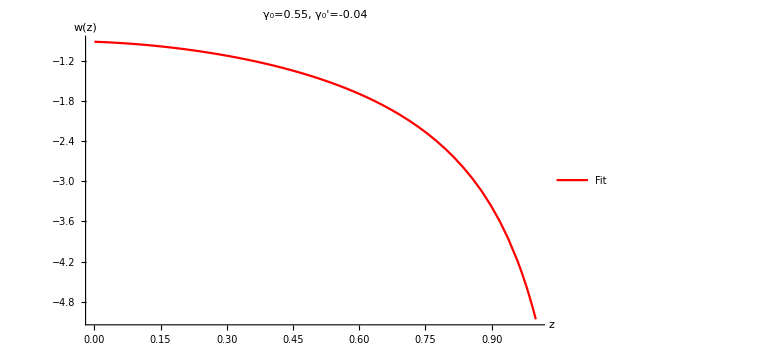

```mathematica
wpol=Plot[wpoly[z],{z,0,1},PlotLegends->{"Fit"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Red}, ImageSize->Large, PlotLabel->Style["γ_0=0.55, γ_0'=-0.04", Black, FontSize->20]]
```

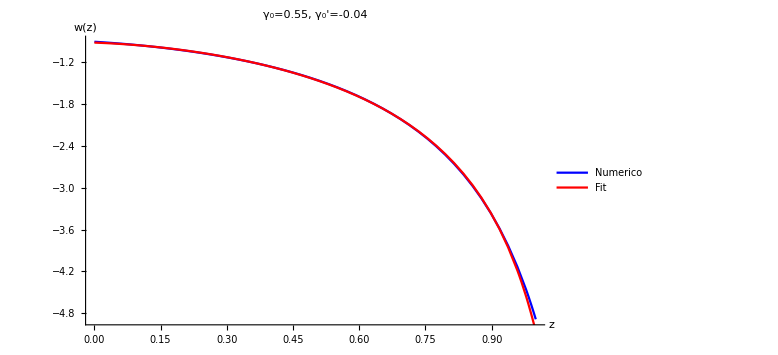

```mathematica
Show[wnum,wpol]
```

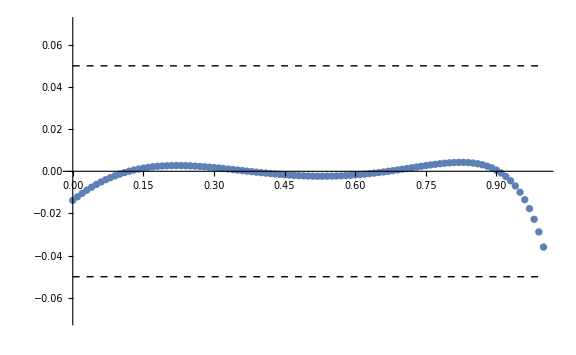

```mathematica
wnumtable=Table[{z,w[z]},{z,0,1,0.01}];
wpoltable=Table[{z,wpoly[z]},{z,0,1,0.01}];
dif1[z_]=1-wpoly[z]/w[z];
Res7=Table[{z,dif1[z]},{z,0,1,0.01}];
plotres=ListPlot[Res7];
errorplot1=Plot[0.05,{z,0,1}, PlotStyle->{Thick, Dashed, Black}];
errorplot2=Plot[-0.05,{z,0,1}, PlotStyle->{Thick, Dashed, Black}];
Show[plotres,errorplot1,errorplot2, PlotRange->{-0.07,0.07}, ImageSize->Large]
```

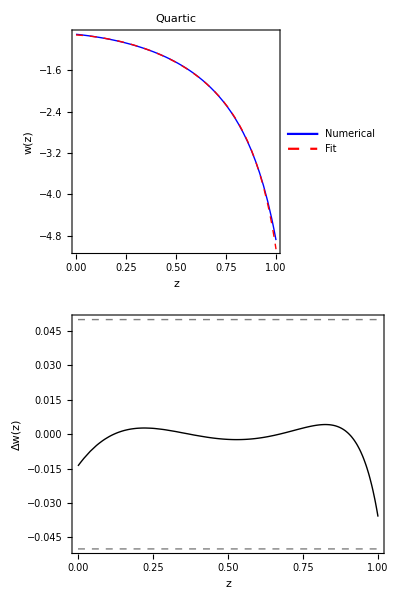

```mathematica
col3=Column[{Plot[{w[z],wpoly[z]},{z,0,1},ImagePadding->{{100,4},{1,1}} ,PlotStyle->{{Thick,Blue},{Thick,Dashed,Red}}, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["w(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"Numerical", "Fit"},LegendFunction->"Frame", Background->White],{Left,Bottom}], PlotLabel->Style["Quartic", Black, FontSize->20]],Plot[{0.05,-0.05, dif1[z]},{z,0,1},ImagePadding->{{100,4},{70,0}},PlotStyle->{{Thick,Dashed,Gray},{Thick,Dashed,Gray}, {Thick, Black}}, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["Δw(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, AspectRatio->1/4, PlotRange->{0.09,-0.09}]}, Spacings->0]
```

```mathematica
Clear
ClearAll
ClearAttributes
ClearCookies
```

Clear

ClearAll

ClearAttributes

ClearCookies

```mathematica
fit4=Fit[points, {1,z},z]
```

1.18398-0.770352 z

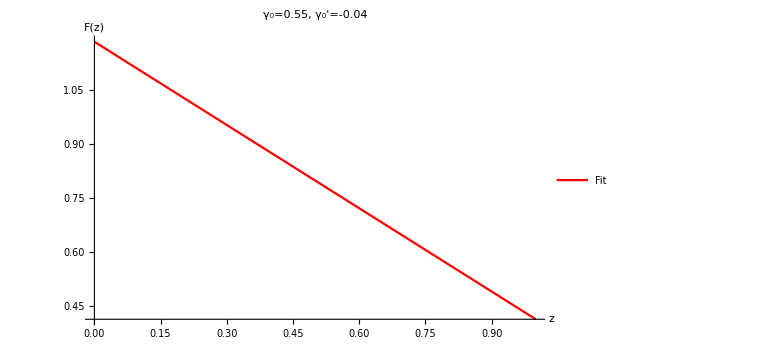

```mathematica
fit=Plot[fit4,{z,0,1}, PlotLegends->{"Fit"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["F(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Red}, ImageSize->Large, PlotLabel->Style["γ_0=0.55, γ_0'=-0.04", Black, FontSize->20]]
```

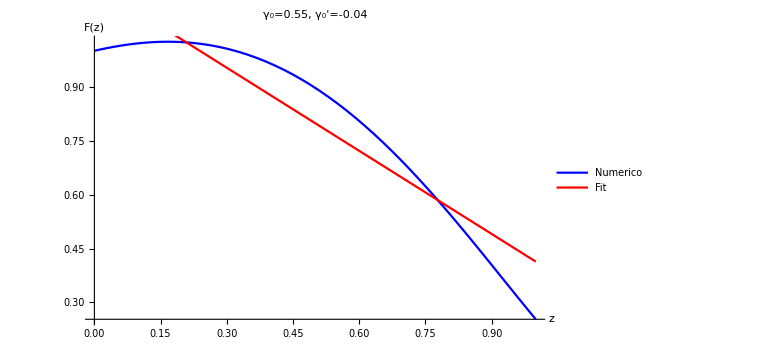

```mathematica
Show[p1,fit]
```

```mathematica
pointsfit4=Table[{z,fit4},{z,0,1,0.01}];
PearsonChiSquareTest[pointsfit4,points]
```

0.500546

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
Fpoly[z_]:=1.1839849560293432-0.7703519993857574 z
```

```mathematica
wnum=Plot[w[z],{z,0,1},PlotLegends->{"Numerico"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Blue}, ImageSize->Large, PlotLabel->Style["γ_0=0.55, γ_0'=-0.04", Black, FontSize->20]]
```

-Graphics-

```mathematica
wpoly[z_]:=Fpoly'[z]/Fpoly[z] 1/3(1+z)-1;
```

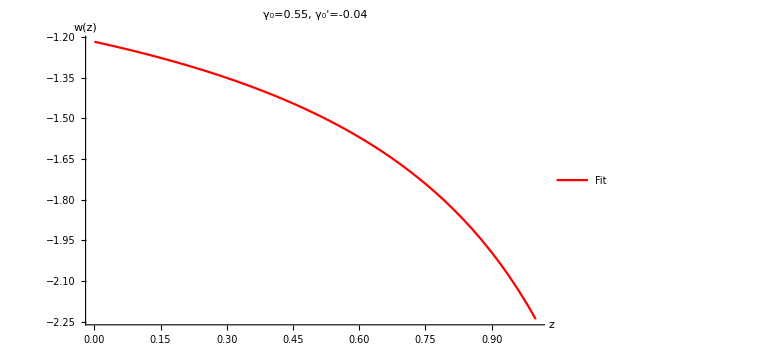

```mathematica
wpol=Plot[wpoly[z],{z,0,1},PlotLegends->{"Fit"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Red}, ImageSize->Large, PlotLabel->Style["γ_0=0.55, γ_0'=-0.04", Black, FontSize->20]]
```

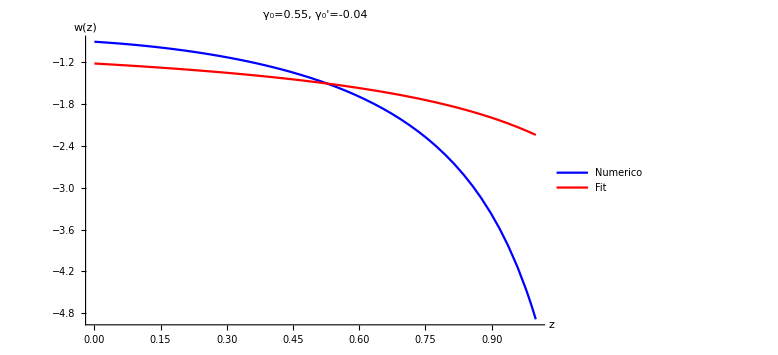

```mathematica
Show[wnum,wpol]
```

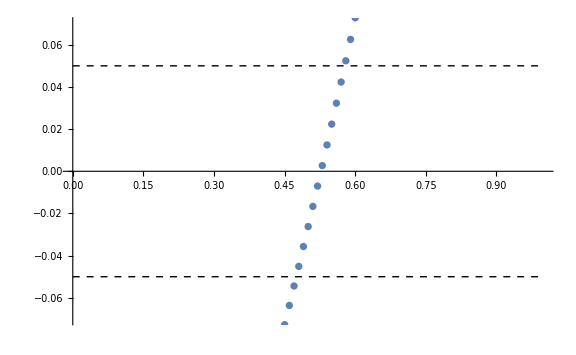

```mathematica
wnumtable=Table[{z,w[z]},{z,0,1,0.01}];
wpoltable=Table[{z,wpoly[z]},{z,0,1,0.01}];
dif1[z_]=1-wpoly[z]/w[z];
Res7=Table[{z,dif1[z]},{z,0,1,0.01}];
plotres=ListPlot[Res7];
errorplot1=Plot[0.05,{z,0,1}, PlotStyle->{Thick, Dashed, Black}];
errorplot2=Plot[-0.05,{z,0,1}, PlotStyle->{Thick, Dashed, Black}];
Show[plotres,errorplot1,errorplot2, PlotRange->{-0.07,0.07}, ImageSize->Large]
```

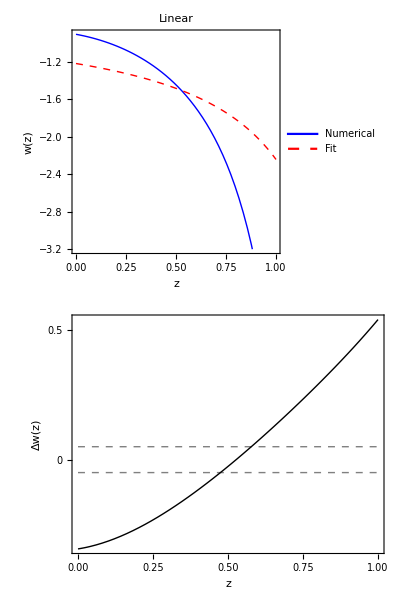

```mathematica
col4=Column[{Plot[{w[z],wpoly[z]},{z,0,1},ImagePadding->{{100,4},{1,1}} ,PlotStyle->{{Thick,Blue},{Thick,Dashed,Red}}, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["w(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"Numerical", "Fit"},LegendFunction->"Frame", Background->White],{Left,Bottom}], PlotRange->{-0.7,-3.2}, PlotLabel->Style["Linear", Black, FontSize->20]],Plot[{0.05,-0.05, dif1[z]},{z,0,1},ImagePadding->{{100,4},{70,0}},PlotStyle->{{Thick,Dashed,Gray},{Thick,Dashed,Gray}, {Thick, Black}}, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["Δw(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, AspectRatio->1/4, PlotRange->{0.6,-0.6}, FrameTicks->{Automatic, {-0.5,0,0.5}}]}, Spacings->0]
```

```mathematica
graph=GraphicsGrid[{{col4,col1}, {col2, col3}}, ImageSize->Full, Spacings->-60]
```

-Graphics-

```mathematica
SetDirectory["C:\\Users\\Gerald\\Desktop\\7sem\\dark energy\\final_plots"]
```

C:\Users\Gerald\Desktop\7sem\dark energy\final_plots

```mathematica
Export["w(z)_poly.png",graph,ImageResolution->500]
```

w(z)_poly.png